# Verify single/multi

```mathematica
SetCurrentDir[]
```

C:\hyapp\PSR-Programs\GitHub\siris4-framework\test\Verify-single-multi\

## 1

```mathematica
s1=Import["single1-S.out","Table"];
%[[{1,-1}]]
```

{{0.,1.05397,-0.00176357,-0.00816864,0.000604925,-0.00128435,0.993373,0.00484822,0.00987172,0.00912003,-0.0128303,0.99049,0.00683781,0.00169559,0.00152585,-0.00488069,1.00829},{180.,0.783309,-0.00250477,0.000218651,-0.00164881,0.010657,0.392176,-0.0119512,0.0149553,-0.000291721,0.00386258,-0.386336,-0.0100821,0.00425562,0.0487327,0.0437498,-0.0918313}}

```mathematica
m1=Import["multi-S.out","Table"];
%[[{1,-1}]]
```

{{0,0.689642,-0.0156496,0.0039476,0.0063615,nan,nan,nan,nan,nan,nan,nan,nan,nan,nan,nan,nan},{180,1.14809,-0.00880698,-0.00193021,0.0165462,0.00747548,0.34815,0.0889333,-0.082067,-0.00643787,-0.130546,-0.549605,-0.189939,0.00627771,-0.0525223,0.052828,0.052759}}

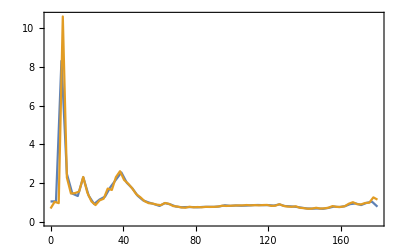

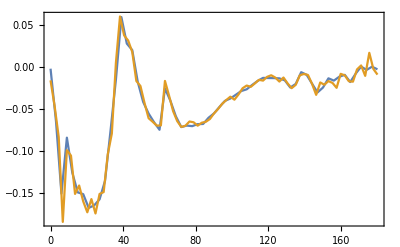

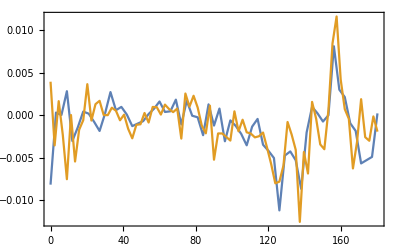

```mathematica
ListPlot[{s1[[All,{1,2}]],m1[[All,{1,2}]]},PlotRange->All]
ListPlot[{s1[[All,{1,3}]],m1[[All,{1,3}]]},PlotRange->All]
ListPlot[{s1[[All,{1,4}]],m1[[All,{1,4}]]},PlotRange->All]
```

## 2

### Separate

Qsca and abs

```mathematica
{qs1,qa1}=Import["single1-Q.out","Table"][[{1,2},-1]]
{qs2,qa2}=Import["single2-Q.out","Table"][[{1,2},-1]]
{qsa,qaa}=Mean[{%%,%}]
```

{0.908589,0.091295}

{0.908977,0.0907511}

{0.908783,0.091023}

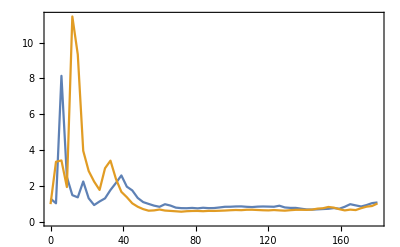

```mathematica
mm1=Import["single1-S.out","Table"];
mm2=Import["single2-S.out","Table"];
ListPlot[{mm1[[All,{1,2}]],mm2[[All,{1,2}]]},PlotRange->All]
```

12.5664

12.5283

12.566

12.5472

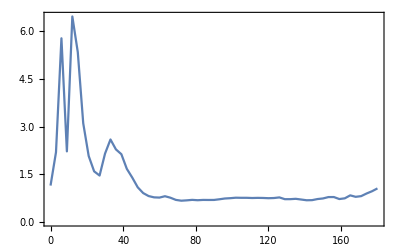

```mathematica
4. π
Csca[mm1]
Csca[mm2]
mma=Mean[{mm1,mm2}];
Csca[mma]
ListPlot[ mma[[All,{1,2}]],PlotRange->All]
```

### Together

```mathematica
g1=Import["vg1.off"]
g2=Import["vg2.off"]
```

-Graphics3D-

-Graphics3D-

```mathematica
sd=1.25;
gt=Graphics3D[ {Translate[ g1,{-sd,0,0}],Translate[ g2,{sd,0,0}]}]
```

-Graphics3D-

```mathematica
Export["vgt-1.25.off",gt,"BinaryFormat"->False]
```

vgt-1.25.off

```mathematica
mmt10=Import["multit-10-S.out","Table"];
```

```mathematica
mmt5=Import["multit-5-S.out","Table"];
```

```mathematica
mmt3=Import["multit-3-S.out","Table"];
```

```mathematica
mmt2=Import["multit-2-S.out","Table"];
```

```mathematica
mmt15=Import["multit-1.5-S.out","Table"];
```

```mathematica
mmt125=Import["multit-1.25-S.out","Table"];
```

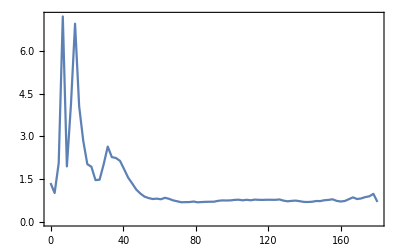

```mathematica
ListPlot[%[[All,{1,2}]],PlotRange->All]
```

### Compare

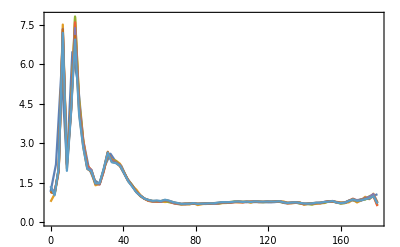

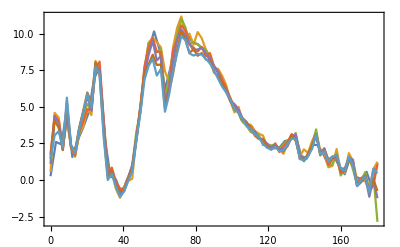

```mathematica
t={mma,mmt10,mmt5,mmt3,mmt2,mmt15,mmt125};
ListPlot[Map[#[[All,{1,2}]] &, t],PlotRange->All]
ListPlot[Map[DoLP[#,"P21"->6] &, t],PlotRange->All]
```